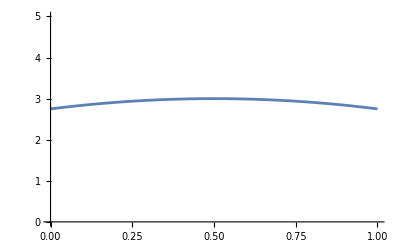

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{0.0790391,0.239859,0.40981}

```mathematica
f=x↦-(x-0.5)^2+3;
Plot[f[x],{x,0,1}, PlotRange->{0,5}]
μ=1;
```

```mathematica
DampingAndFreq={kn,cn,mn}↦{cn/(2√(mn kn)),√(kn/mn)};
SpringMassDamper={ζn,ωn}↦Hn↦{Xdd,θdd,θ}↦{xn,xndot}↦
{xndot,-2ζn ωn xndot-ωn^2 xn-Xdd-Hn θdd+9.81θ};

CofMassLateralDisplacement={xVec,R}↦1/6(Total[xVec]+3R)-0.5R;
ActualAngularAccelerationUpdate={M,m0,H0,Ht,mVec,xVec,xddVec,hVec,τ}↦
(Total[mVec*hVec(xddVec)]-9.81(mVec.xVec)+M)/(τ(m0 (Ht^2+H0^2)+Total[mVec*hVec^2]));

nonLinear1={α,β,γ,y0,y1}↦x↦Log[γ+α E^(β x^2)]-Log[γ+α]+y0;
nonLinear2={α,β,γ,y0,y1}↦x↦(y1-y0)((1+α E^(-β(Abs[x]-γ)))^(-1)-(1+α E^(β γ))^(-1))+y0;

findCOM={lower,upper,f}↦(Integrate[x f[x]^2,{x,lower,upper}])/(Integrate[f[x]^2,{x,lower,upper}]);
extractHVec={COM,otherBoundaries,μ,f,h}↦
{h(findCOM[COM,otherBoundaries[[1]],f]-COM),
h(findCOM[otherBoundaries[[1]],otherBoundaries[[2]],f]-COM),
h(findCOM[otherBoundaries[[2]],μ,f]-COM)};
findRadiusVals={zVec,f}↦{f[zVec[[1]]],f[zVec[[2]]],f[zVec[[3]]]};
```

```mathematica
Manipulate[
Module[
{ζn,ωn,trajectory,xddVec,xVec,hVec,mVec,R1,R2,R3,mn,TotalVolume},

StiffnessEquation=nonLinear2[αx,βx,γx,y0x,y1x][x];
DampingEquation=nonLinear1[αxd,βxd,γxd,y0xd,y1xd][xd];
{ζn,ωn}=DampingAndFreq[StiffnessEquation,DampingEquation,mn];

SystemParamsSet=SpringMassDamper[ζn,ωn];
system1=SystemParamsSet[5][Xdd,θ''[t],θ[t]][x1[t],x1'[t]][[2]]/.{x->x1[t],xd->x1'[t]};
system2=SystemParamsSet[3][Xdd,θ''[t],θ[t]][x2[t],x2'[t]][[2]]/.{x->x2[t],xd->x2'[t]};
system3=SystemParamsSet[1][Xdd,θ''[t],θ[t]][x3[t],x3'[t]][[2]]/.{x->x3[t],xd->x3'[t]};

f=x↦-(x-0.5)^2+3;

V1=Integrate[f[x]^2,{x,xCOM,x1Bound}];
V2=Integrate[f[x]^2,{x,x1Bound,x2Bound}];
V3=Integrate[f[x]^2,{x,x2Bound,μ}];
Results=Quiet[Solve[{V1==V2,V1==V3},{x1Bound,x2Bound},Reals]];

xCOM=findCOM[0,μ,f];
MassBounds=Flatten[{x1Bound,x2Bound}/.Results];
hVec=extractHVec[xCOM,MassBounds,μ,f,1];
zVec=hVec+xCOM h;
{R1,R2,R3}=findRadiusVals[zVec,f];

TotalVolume=Integrate[f[x]^2,{x,0,μ}];
mn=TotalVolume/6;
mVec={mn,mn,mn};

angular=ActualAngularAccelerationUpdate[M,3mn,xCOM/2,(h-xCOM)/2,mVec,{x1[t],x2[t],x3[t]},{x1''[t],x2''[t],x3''[t]},hVec,τ];
collisionEquation=x↦-λ x;

trajectory=Quiet@NDSolve[{
x1'[t]==x1dot[t],x2'[t]==x2dot[t],x3'[t]==x3dot[t],
x1''[t]==system1,x2''[t]==system2,x3''[t]==system3,
x1[0]==x1Var,x1dot[0]==x1dVar,x2[0]==x2Var,x2dot[0]==x2dVar,x3[0]==x3Var,x3dot[0]==x3dVar,
θ'''[t]==angular,θ[0]==θVar,θ'[0]==θdVar,θ''[0]==θddVar,
WhenEvent[x1[t]>=R1,{x1dot[t]->collisionEquation[x1dot[t],-1],x1[t]->R1}],
WhenEvent[x2[t]>=R2,{x2dot[t]->collisionEquation[x2dot[t],-1],x2[t]->R2}],
WhenEvent[x3[t]>=R3,{x3dot[t]->collisionEquation[x3dot[t],-1],x3[t]->R3}],
WhenEvent[x1[t]<=-R1,{x1dot[t]->collisionEquation[x1dot[t],1],x1[t]->-R1}],
WhenEvent[x2[t]<=-R2,{x2dot[t]->collisionEquation[x2dot[t],1],x2[t]->-R2}],
WhenEvent[x3[t]<=-R3,{x3dot[t]->collisionEquation[x3dot[t],1],x3[t]->-R3}]},
{x1,x1dot,x2,x2dot,x3,x3dot,θ},
{t,0,tmax}
];
fluidMomentData=Table[{t,
FluidExertedMoment[
3mn,3,6,θdd,
{mn,mn,mn},
Flatten[{x1[t],x2[t],x3[t]}/. trajectory],
Flatten[{a1[t],a2[t],a3[t]}/. trajectory],
{5,3,1} ]},
{t,0,tmax,tmax/100} 
];
centreOfMassData=Table[{t,
CofMassLateralDisplacement[
Flatten[{x1[t],x2[t],x3[t]}/. trajectory],{R1,R2,R3}]},
{t,0,tmax,tmax/100} 
];
DisplacementPlot=Plot[
Evaluate[{x1[t],x2[t],x3[t]}/. trajectory],
{t,0,tmax},
PlotStyle->{Thick,Red,Blue,Green},
PlotLegends->{"x1[t]","x2[t]","x3[t]"},
AxesLabel->{"Time","Position (x)"},
PlotRange->All
];
VelocityPlot=Plot[
Evaluate[{x1dot[t],x2dot[t],x3dot[t]}/. trajectory],
{t,0,tmax},
PlotStyle->{Thick,Red,Blue,Green},
PlotLegends->{"x1'[t]","x2'[t]","x3'[t]"},
AxesLabel->{"Time","Velocity (x')"},
PlotRange->All
];
AnglePlot=Plot[
Evaluate[θ[t]/. trajectory],
{t,0,tmax},
PlotStyle->{Thick,Blue},
PlotRange->All
];
streamPlot=StreamPlot[
SystemParamsSet[5][Xdd,θdd,θ][xn,xndot],
{xn,-5,5},
{xndot,-5,5},
StreamStyle->Arrowheads[0.02]
];
ParametricTrajectoryPlot=ParametricPlot[
Evaluate[
{{x1[t],x1dot[t]}/. trajectory,
{x2[t],x2dot[t]}/. trajectory,
{x3[t],x3dot[t]}/. trajectory}],
{t,0,tmax},
PlotStyle->{Thick,Red,Blue,Green},
PlotLegends->{"x1[t]","x2[t]","x3[t]"},
AxesLabel->{"x","x'"},
PlotRange->All
];
combinedTrajectoryPlot=ParametricPlot[
Evaluate[{
{x1[t],x1dot[t]}/. trajectory,
{x2[t],x2dot[t]}/. trajectory,
{x3[t],x3dot[t]}/. trajectory }],
{t,0,tmax},
PlotStyle->{Thick,Red,Blue,Green},
PlotLegends->{"x1","x2","x3"},
PlotRange->{{-5,5},{-10,10}},
AspectRatio->1
];
momentPlot=ListPlot[
fluidMomentData,
Joined->True,
PlotStyle->Thick,
AxesLabel->{"Time","Fluid Moment"},
PlotRange->All
];
CofMassPlot=ListPlot[
centreOfMassData,
Joined->True,
PlotStyle->Thick,
AxesLabel->{"Time","Centre of Mass Location"},
PlotRange->All
];
StreamPlotXandXd=StreamPlot[
SystemParamsSet[5][Xdd,θddVar,θVar][x,xd],
{x,-5,5},
{xd,-10,10},
StreamStyle->Arrowheads[0.02],
StreamPoints->Fine,
FrameLabel->{"x (position)","v (velocity)"},
PlotRange->All];
StiffnessPlot=Plot[
StiffnessEquation,
{x,-5,5},
AxesLabel->{"Displacement","Stiffness Coefficient"},
PlotRange->{{-5,5},{0,20}}];
DampingPlot=Plot[
DampingEquation,
{xd,-10,10},
AxesLabel->{"Velocity","Damping Coefficient"},
PlotRange->{{-10,10},{0,20}}];
GraphicsRow[{DampingPlot,StreamPlotXandXd}]
],
(*{{kn,1,"kn"},0,100,0.1},
{{cn,10,"cn"},0,100,0.1},*)
(*{{mn,1,"mn"},0.1,5,0.1},*)
{{x1Var,0,"x1"},-R,R,0.1},
{{x1dVar,0,"x1dot"},-10,10,0.1},
{{x2Var,0,"x2"},-R,R,0.1},
{{x2dVar,0,"x2dot"},-10,10,0.1},
{{x3Var,0,"x3"},-R,R,0.1},
{{x3dVar,0,"x3dot"},-10,10,0.1},
{{tmax,50,"Time Range"},1,1000,5} ,
{{Xdd,0,"Xdd"},-5,5,0.1},
{{θVar,0,"θ"},-0.5,0.5,0.05},
{{θdVar,0,"θd"},-0.5,0.5,0.05},
{{θddVar,0,"θdd"},-5,5,0.1},
{{λ,0.1,"λ"},0,1,0.05},
{{μ,0.8,"μ'"},0,1,0.01},
{{h,10,"h'"},0,20,0.5},
{{M,0,"M"},0,10,0.05},
{{τ,10000,"τ"},0,50000,100},
{{αx,1,"α_x"},0,10,0.5},
{{βx,5,"β_x"},0,10,0.5},
{{γx,2,"γ_x"},0,10,0.5},
{{y0x,1,"y0_x"},0,10,0.05},
{{y1x,10,"y1_x"},0,20,0.5},
{{αxd,1,"α_x'"},0,10,0.1},
{{βxd,5,"β_x'"},0,10,0.1},
{{γxd,2,"γ_x'"},0,10,0.5},
{{y0xd,1,"y0_x'"},0,10,0.05},
{{y1xd,10,"y1_x'"},0,20,0.5}
]
```